## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Сучков А.Р. Группа: ТФ-13-22 Задача № 1 -Graphics-

#### Данные из условия: d2=120(mm);δ=4(mm) - геометрия труб ; tAir=2 (°C)-температура воздуха;tLiquid1=160(°C)-температура горячей воды на входе (как t_ж1) ; p=5(MPa)- давление горячей воды;w=5(km/h) - скорость течения горячей воды; λMinWool=0.055(W/m*K);δMinWool=30(mm); tLiquid2=160-60=100(°C)-температура горячей воды на выходе(как t_ж2) ; λConcrete=1.1(W/m K);δConcrete=30(mm);ϵ=0.8-излучательная способность поверхности материала труб; α= 12.2(W/m^2K)-коэффициент теплоотдачи

```mathematica
d2=120*10^-3;δ=4*10^-3;tAir=2;tLiquid1=160;p=5*10^6;w=5/3.6;λMinWool=0.055;δMinWool=30*10^-3;tLiquid2=100;λConcrete=1.1;δConcrete=30*10^-3;
ϵ=0.8;
α=12.2;
```

#### Сталь берем нержавеющую, ее коэффициент теплопроводности λSteel (W/m K) берем как const в виду слабой зависимости от температуры:

```mathematica
λSteel=14.4 ;
```

#### Изобарную (p=5MPa)теплоемкость и плотность воды при tLiquid1 и tLiquid2 найдем через REFPROP: cp: tLiquid1=160 (°C) =433.15(K) cp1=4.3204 (kJ/kg K) -Graphics-

#### tLiquid2=100 (°C) =373.15(K) cp2=4.2029 (kJ/kg K) -Graphics- плотность: tLiquid1=160 (°C) ρ1=910.03 (kg/m^3) -Graphics- tLiquid2=100 (°C) ρ2=960.60 (kg/m^3) -Graphics-

```mathematica
cp1=4.3204;cp2=4.2029 ;ρ1=910.03;ρ2=960.60 ;
```

#### Средняя удельная изобарная теплоемкость cpAverage(J/kg K)

```mathematica
cpAverage=(cp1+cp2)/2*1000
```

4261.65

#### Средняя плотность воды ρAverage (kg/m^3)

```mathematica
ρAverage=(ρ1+ρ2)/2
```

935.315

#### Массовый расход воды G(kg/s)

```mathematica
G=π*((d2-2*δ)/2)^2*w*ρAverage
```

12.7983

#### Найдем диаметры d1, d3 (m)

```mathematica
d1=d2-2δ//N
```

0.112

```mathematica
d3=d2+2δ//N
```

0.128

#### Найдем линейный коэффициент теплопередачи для трубы с ватной изоляцией KlinearMinWool (W/m K)

```mathematica
KlinearMinWool=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/(α*d3))
```

0.509859

#### Применяя формулу Шухова найдем расстояние(длину трубы) на котором будет выполняться условие разности температур на входе и выходе в трубу с изоляцией из минеральной ваты:

```mathematica
L=First[NSolveValues[tLiquid2==tAir+(tLiquid1-tAir)*Exp[-KlinearMinWool/(G*cpAverage)*π*x],x]]
```

16263.7

#### Найдем линейный коэффициент теплопередачи для трубы с бетонной изоляцией KlinearConcrete (W/m K)

```mathematica
KlinearConcrete=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/(α*d3))
```

0.712276

#### По формуле Шухова найдем температуру на выходе из трубы с бетонной изоляцией:

```mathematica
t[x_,k_]:=tAir+(tLiquid1-tAir)*Exp[-k/(G*cpAverage)*π*x]
```

```mathematica
t[L,KlinearConcrete]
```

83.0727

#### Найдем линейный коэффициент теплопередачи для трубы без изоляции KlinearRaw (W/m K)

```mathematica
KlinearRaw=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(α*d3))
```

0.727477

#### По формуле Шухова найдем температуру на выходе из трубы без изоляции:

```mathematica
t[L,KlinearRaw]
```

81.9264

#### Функция теплового потока и плотности теплового потока :

```mathematica
Q[x_,k_]:=k*π*(t[x,k]-tAir)*x;
qLinear[x_,k_]:=k*π*(t[x,k]-tAir);
```

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для голой трубы:

```mathematica
Q[L,KlinearRaw]
```

2.97083×10^6

```mathematica
qLinear[L,KlinearRaw]
```

182.667

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с бетонной изоляцией:

```mathematica
Q[L,KlinearConcrete]
```

2.95047×10^6

```mathematica
qLinear[L,KlinearConcrete]
```

181.415

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с ватной изоляцией:

```mathematica
Q[L,KlinearMinWool]
```

2.55296×10^6

```mathematica
qLinear[L,KlinearMinWool]
```

156.973

### Произведем расчеты по другому:

```mathematica
qLinearAdditional[k_]:=k*π*((tLiquid1+tLiquid2)/2-tAir)
```

#### Запишем баланс энергий: Q=qLinear*L=G*cpAverage*(tLiquid1-tLiquid2)=π *(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),отсюда можно найти L(m):

```mathematica
Ladditional=First[NSolveValues[qLinearAdditional[KlinearMinWool]*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),x]]
```

15961.4

#### Выразим tLiquid2 из линейной плотности теплового потока как переменную :

```mathematica
Solve[k*π*((tLiquid2asVariable+tLiquid1)/2-tAir)*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2asVariable),tLiquid2asVariable]
```

{{tLiquid2asVariable→(8.72668×10^6-245.044 k x)/(54541.8+1.5708 k x)}}

```mathematica
tLiquid2asVariable[k_,x_]:=(8.72668*10^6-245.044227 k* x)/(54541.75506+1.570796* k *x)
```

#### Теперь найдем температуры на выходе из трубы с бетонной изоляцией и трубы без изоляции. Бетонная изоляция:

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

82.0551

#### Голая труба:

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

80.8086

#### Изобразим функциональные зависимости температуры жидкости в точке χ, где χ-обобщенное расстояние(от точки входа воды)

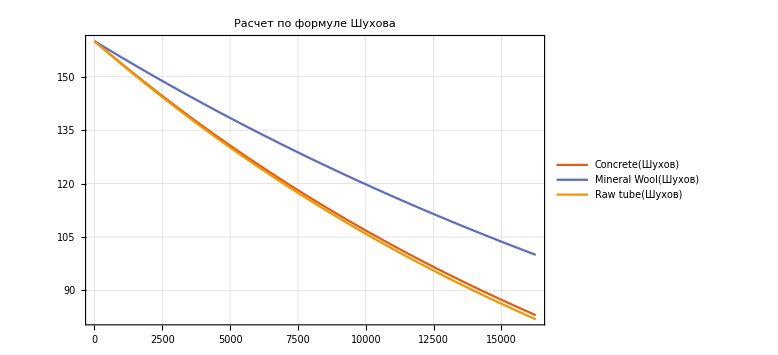

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw]},{χ,0,L},PlotLabel->"Расчет по формуле Шухова",PlotTheme->"Scientific",PlotLegends->{"Concrete(Шухов)","Mineral Wool(Шухов)","Raw tube(Шухов)"},ImageSize->Large,GridLines->Automatic]
```

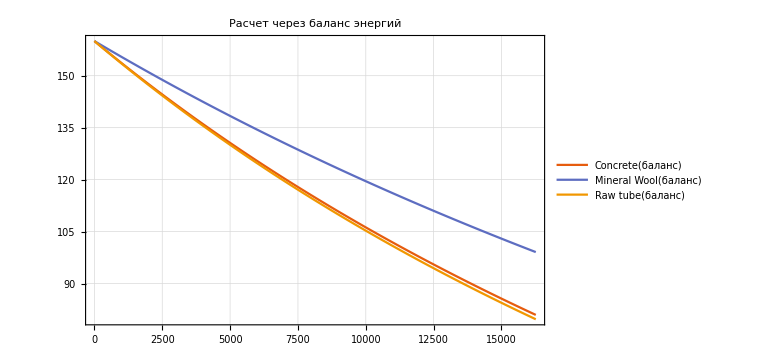

```mathematica
Plot[{tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Расчет через баланс энергий",PlotTheme->"Scientific",PlotLegends->{"Concrete(баланс)","Mineral Wool(баланс)","Raw tube(баланс)"},ImageSize->Large,GridLines->Automatic]
```

#### Сопоставим функции температур в одной системе координат:

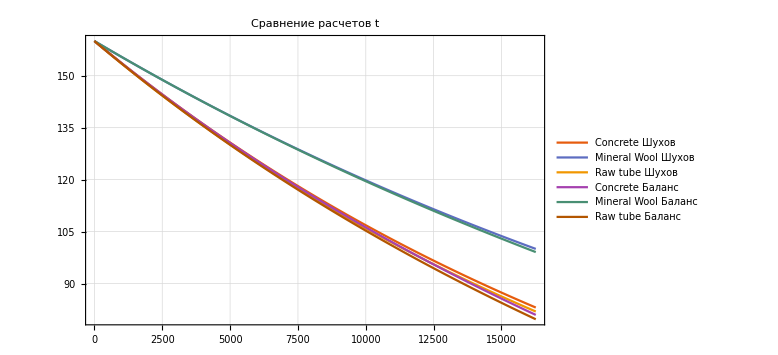

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Точно так же изобразим функции линейных плотностей тепловых потоков. Для начала введем функцию линейной плотности теплового потока при расчете методом баланса энергий:

```mathematica
qLinearAdditionalFunction[k_]:=k*π*((tLiquid1-tLiquid2)/2-tAir)
```

#### Покажем графики линейных плотностей тепловых потоков в одной координатной плоскости ql(W/m):

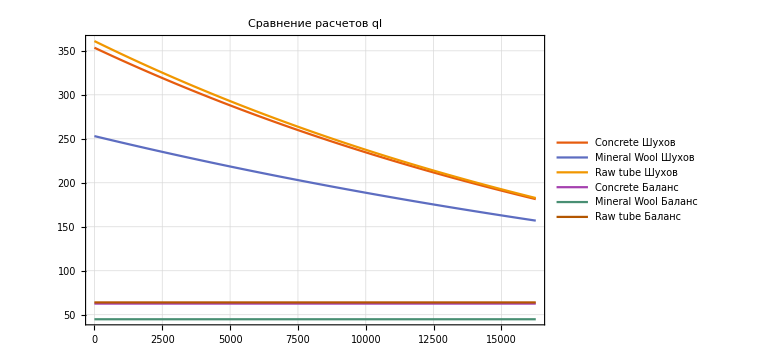

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearAdditionalFunction[KlinearConcrete],qLinearAdditionalFunction[KlinearMinWool],qLinearAdditionalFunction[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов ql",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Теперь построим поверхностные плотности тепловых потоков qc (W/m^2):

```mathematica
qcShuhov[x_,k_]:=qLinear[x,k]/(π*d1);qcBalance[k_]:=qLinearAdditionalFunction[k]/(π*d1);
```

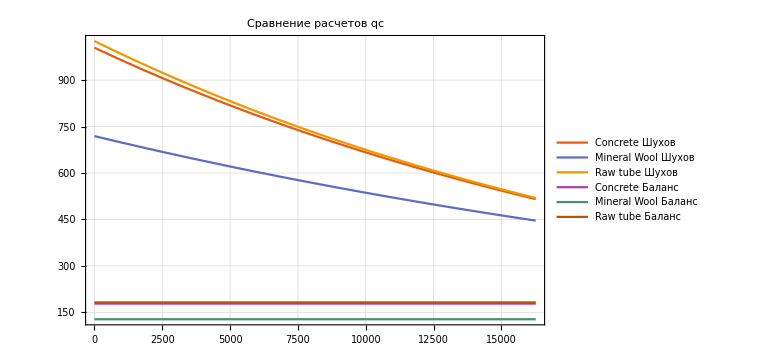

```mathematica
Plot[{qcShuhov[χ,KlinearConcrete],qcShuhov[χ,KlinearMinWool],qcShuhov[χ,KlinearRaw],qcBalance[KlinearConcrete],qcBalance[KlinearMinWool],qcBalance[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов qc",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Найдем среднее значение линейной плотности теплового потока(W/m):

```mathematica
qLinearAverageWithoutInsulation=(qLinear[0,KlinearRaw]+qLinear[L,KlinearRaw])/2
```

271.883

```mathematica
qLinearAverageConcreteInsulation=(qLinear[0,KlinearConcrete]+qLinear[L,KlinearConcrete])/2
```

267.484

```mathematica
qLinearAverageMinWoolInsulation=(qLinear[0,KlinearMinWool]+qLinear[L,KlinearMinWool])/2
```

205.026

#### Среднее значение температуры на поверхности труб:

```mathematica
{twWithoutIns,twConcreteIns,twMinWoolIns}=Flatten[NSolveValues[{qLinearAverageWithoutInsulation==π*(twWithoutInsBUFFER-tAir)/(1/(α*d2)),qLinearAverageConcreteInsulation==π*(twConcreteInsBUFFER-tAir)/(1/(α*d3)),qLinearAverageMinWoolInsulation==π*(twMinWoolInsBUFFER-tAir)/(1/(α*d3))},{twWithoutInsBUFFER,twConcreteInsBUFFER,twMinWoolInsBUFFER}]]
```

{61.114,56.5228,43.7917}

#### Учтем излучение σ- константа Стефана-Больцмана(W/m^2 K^4)

```mathematica
σ=5.671*10^-8;
```

#### Переведем температуры на поверхности труб и температуру воздуха в абсолютные единицы(Кельвины)

```mathematica
TwWithoutIns=twWithoutIns+273.15;TwConcreteIns=twConcreteIns+273.15;TwMinWoolIns=twMinWoolIns+273.15;Tair=tAir+273.15;
```

#### Найдем результирующую плотность потока излучения Eres(W/m^2):

```mathematica
EresMinWool=ϵ*σ*(TwMinWoolIns^4-Tair^4)
```

197.758

```mathematica
EresConcrete=ϵ*σ*(TwConcreteIns^4-Tair^4)
```

275.866

```mathematica
EresWithoutIns=ϵ*σ*(TwWithoutIns^4-Tair^4)
```

306.348

#### Найдем эквивалентный коэффициент теплоотдачи излучением αEqv (W/m^2K):

```mathematica
αEqvMinWool=EresMinWool/(TwMinWoolIns-Tair)
```

4.732

```mathematica
αEqvConcrete=EresConcrete/(TwConcreteIns-Tair)
```

5.05963

```mathematica
αEqvWithoutIns=EresWithoutIns/(TwWithoutIns-Tair)
```

5.18232

```mathematica
MradMinWool=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/((α+αEqvMinWool)*d3)
```

1.78236

```mathematica
MradConcrete=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3)
```

1.21623

```mathematica
MradWithoutIns=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3)
```

1.1837

```mathematica
P=(d1/2)^2*w*ρAverage*cpAverage
```

17361.2

```mathematica
tLiquid2RadiationVariable[M_,x_]:=(2*P*M*tLiquid1+2*tAir*x - tLiquid1*x)/(x+2*P*M)
```

#### Линейная плотность потока излучения для трубы с ватной изоляцией:

```mathematica
qLinearRadiationMinWool[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradMinWool,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))
```

#### Из баланса энергий найдем длину трубы:

```mathematica
LwithRadiation=First[NSolveValues[((tLiquid1+tLiquid2)/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))*Len ==π*(d1/2)^2*w*ρAverage*cpAverage*(tLiquid1-tLiquid2),Len]]
```

31318.5

#### Линейная плотность потока излучения трубы с ватной изоляцией:(W/m)

```mathematica
qLinearRadiationMinWool[LwithRadiation]
```

269.052

#### Для трубы без изоляции:(W/m)

```mathematica
qLinearRadiationWithoutIns[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradWithoutIns,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3))
```

```mathematica
qLinearRadiationWithoutIns[LwithRadiation]
```

237.992

```mathematica
tLiquid2RadiationVariableWithoutIns=tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

23.3422

#### Для трубы с изоляцией из бетона:

```mathematica
qLinearRadiationConcrete[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradConcrete,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3))
```

```mathematica
qLinearRadiationConcrete[LwithRadiation]
```

234.337

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

25.441

#### Рассчитаем потери теплоты:

```mathematica
QradConcrete[x_]:=qLinearRadiationConcrete[x]*x;
QradMinWool[x_]:=qLinearRadiationMinWool[x]*x;
QradWithoutIns[x_]:=qLinearRadiationWithoutIns[x]*x;
```

#### Потери теплоты в трубе с бетонной изоляцией:(W)

```mathematica
QradConcrete[LwithRadiation]
```

7.33909×10^6

#### Потери теплоты в трубе с ватной изоляцией:(W)

```mathematica
QradMinWool[LwithRadiation]
```

8.4263×10^6

```mathematica
QradWithoutIns[LwithRadiation]
```

7.45356×10^6

#### Сравним расчеты температуры(Шухов/Излучение):

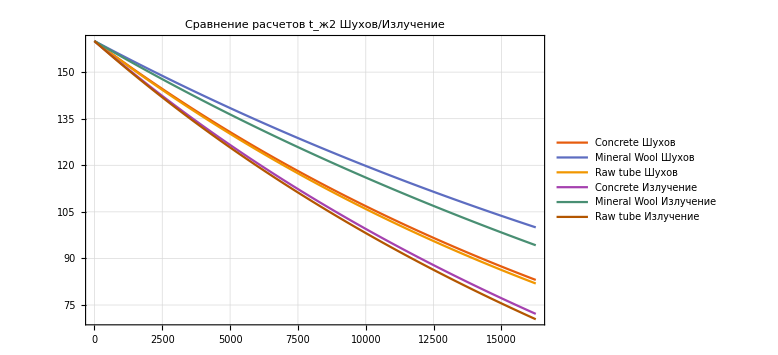

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2RadiationVariable[MradConcrete,χ],tLiquid2RadiationVariable[MradMinWool,χ],tLiquid2RadiationVariable[MradWithoutIns,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t_(:04362) Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Сравним расчеты линейной плотности потоков тепла/излучения(Шухов/Излучение):

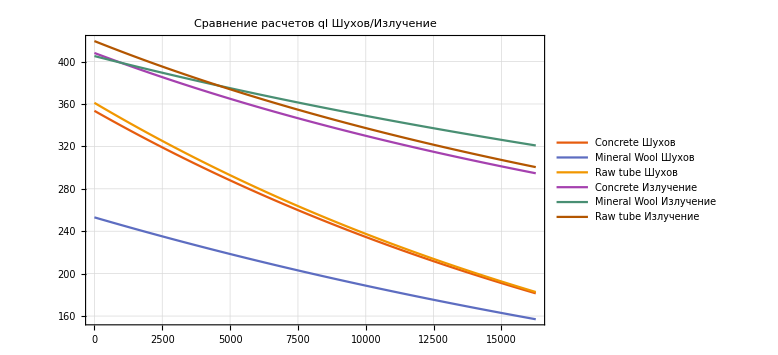

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearRadiationConcrete[χ],qLinearRadiationMinWool[χ],qLinearRadiationWithoutIns[χ]},{χ,0,L},PlotLabel->"Сравнение расчетов ql Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Соберем все результаты выше воедино. Способ основанный на формуле Шухова. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
t[L,KlinearConcrete]
```

83.0727

```mathematica
t[L,KlinearMinWool]
```

100.

```mathematica
t[L,KlinearRaw]
```

81.9264

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Q[L,KlinearConcrete]
```

2.95047×10^6

```mathematica
Q[L,KlinearMinWool]
```

2.55296×10^6

```mathematica
Q[L,KlinearRaw]
```

2.97083×10^6

#### Способ основанный на методе баланса энергии. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции).

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

82.0551

```mathematica
tLiquid2asVariable[KlinearMinWool,Ladditional]
```

100.

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

80.8086

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Qadditional[k_,x_]:=qLinear[x,k]*x;
```

```mathematica
Qadditional[KlinearConcrete,Ladditional]
```

2.93177×10^6

```mathematica
Qadditional[KlinearMinWool,Ladditional]
```

2.52785×10^6

```mathematica
Qadditional[KlinearRaw,Ladditional]
```

2.95278×10^6

#### Способ с учетом излучения.Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

25.441

```mathematica
tLiquid2RadiationVariable[MradMinWool,LwithRadiation]
```

53.82

```mathematica
tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

23.3422

#### Поток излучения(W):(порядок:бетон,вата,без изоляции)

```mathematica
QradConcrete[LwithRadiation]
```

7.33909×10^6

```mathematica
QradMinWool[LwithRadiation]
```

8.4263×10^6

```mathematica
QradWithoutIns[LwithRadiation]
```

7.45356×10^6

#### Найдем критический диаметр при бетонной и ватной изоляциях

```mathematica
d2//N
```

0.12

```mathematica
dCriticalConcrete=d2+(2λConcrete)/α
```

0.300328

```mathematica
dCriticalMinWool=d2+(2λMinWool)/α
```

0.129016

#### Вывод: Тепло от теплоносителя лучше всего сохраняет труба с ватной изоляцией. На втором месте бетон. На почетном третьем- труба без изоляции